```mathematica
SetDirectory@NotebookDirectory[];
Import["QuESTlink.m"];
CreateLocalQuESTEnv["quest_link"];
```

## Parameters

```mathematica
model=0;(*0:Depol;1:Deph;2:Damp;*)
numQb=10;
numGt=numQb^2;
seed=196596;
ϵ=0.002;
SamSize=10000;
```

```mathematica
CreateFile["CS-m"<>ToString[model]<>"-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-e"<>ToString[ϵ]<>".dat"];
file=File["CS-m"<>ToString[model]<>"-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-e"<>ToString[ϵ]<>".dat"];
Data={};
AppendTo[Data,"model:"<>ToString[model]];
AppendTo[Data,"numQb:"<>ToString[numQb]];
AppendTo[Data,"numGt:"<>ToString[numGt]];
AppendTo[Data,"seed:"<>ToString[seed]];
AppendTo[Data,"eps:"<>ToString[ϵ]];
AppendTo[Data,"SamSize:"<>ToString[SamSize]];
AppendTo[Data,""];
Export[file,Data];
```

## QC

```mathematica
ψIN=CreateQureg[numQb];
ψOUT=CreateQureg[numQb];
ψWP=CreateQureg[numQb];
ρIN=CreateDensityQureg[numQb];
ρOUT=CreateDensityQureg[numQb];
ρWP=CreateDensityQureg[numQb];
```

## Gates

```mathematica
PZ={{1.,0.},{0.,-1.}};
PX={{0.,1.},{1.,0.}};
PY={{0.,-ⅈ},{ⅈ,0.}};
iden=IdentityMatrix[2];
Clifford={iden,PX,PY,PZ,(iden+ⅈ PX)/Sqrt[2],(iden-ⅈ PX)/Sqrt[2],(iden+ⅈ PY)/Sqrt[2],(iden-ⅈ PY)/Sqrt[2],(iden+ⅈ PZ)/Sqrt[2],(iden-ⅈ PZ)/Sqrt[2],(PX+PY)/Sqrt[2],(PX-PY)/Sqrt[2],(PX+PZ)/Sqrt[2],(PX-PZ)/Sqrt[2],(PY+PZ)/Sqrt[2],(PY-PZ)/Sqrt[2],(ⅈ iden+PX+PY+PZ)/2,(ⅈ iden-PX-PY+PZ)/2,(ⅈ iden+PX-PY-PZ)/2,(ⅈ iden-PX+PY-PZ)/2,(-ⅈ iden+PX+PY+PZ)/2,(-ⅈ iden-PX-PY+PZ)/2,(-ⅈ iden+PX-PY-PZ)/2,(-ⅈ iden-PX+PY-PZ)/2};
```

```mathematica
gates=Table[IdentityMatrix[2],numQb+2*numGt];
```

## Circuits

```mathematica
GateGraphGen[numQb_,numGt_,seed_]:=(
GateGraph={};
If[seed==-1,
depth=Ceiling[numGt/Floor[numQb/2]];
qINI=0;
Do[(
Do[(
AppendTo[GateGraph,q];
AppendTo[GateGraph,Mod[q+1,numQb]];
),{q,qINI,numQb-1,2}];
qINI=1-qINI;
),{t,0,depth-1,1}];
AppendTo[GateGraph,Table[0,numQb-1]]
];
If[seed!=-1,
SeedRandom[seed];
Do[(
q=RandomInteger[{0,numQb-1}];
dis=RandomInteger[{1,numQb-1}];
AppendTo[GateGraph,q];
AppendTo[GateGraph,Mod[q+dis,numQb]];
),{t,0,numGt-1,1}];
AppendTo[GateGraph,RandomInteger[{0,1},numQb-1]]
];
Return[GateGraph]
)
GateGraph=GateGraphGen[numQb,numGt,seed]
```

{7,8,8,5,4,7,6,0,5,4,6,4,2,6,7,5,6,4,5,9,7,4,8,6,6,1,2,0,7,6,2,6,8,5,0,8,2,8,0,8,6,8,8,9,6,7,9,7,9,5,3,8,1,5,9,4,2,5,1,7,6,1,2,4,6,0,1,7,7,2,8,4,1,2,6,4,5,8,1,9,2,7,9,4,8,2,0,5,1,0,1,5,6,4,9,6,2,1,3,4,4,1,3,6,2,4,8,0,4,9,8,2,4,5,9,2,1,6,9,8,5,9,2,0,4,1,1,0,0,3,4,8,1,5,9,0,4,9,1,6,9,3,3,9,3,9,6,1,4,8,4,6,3,6,6,9,1,5,0,7,3,2,9,4,1,9,9,4,1,6,0,2,0,1,1,7,2,3,2,7,4,2,8,4,7,2,2,6,5,6,2,0,5,2,9,4,1,2,4,9,{1,1,0,0,1,0,1,1,0}}

```mathematica
circuitIdeal[numQb_,numGt_,GateGraph_,gates_]:=(
circ={};
Do[(
g=gates[[q+1]];
AppendTo[circ,Subscript[U, q][g]];
),{q,0,numQb-1,1}];
Do[(
q1=GateGraph[[2*t+1]];
q2=GateGraph[[2*t+2]];
AppendTo[circ,Subscript[C, q1][Subscript[Z, q2]]];
g=gates[[numQb+2*t+1]];
AppendTo[circ,Subscript[U, q1][g]];
g=gates[[numQb+2*t+2]];
AppendTo[circ,Subscript[U, q2][g]];
),{t,0,numGt-1,1}];
Do[(
If[GateGraph[[2*numGt+1,q]]==1,AppendTo[circ,Subscript[C, q][Subscript[X, 0]]]];
),{q,1,numQb-1,1}];
Return[circ]
)
```

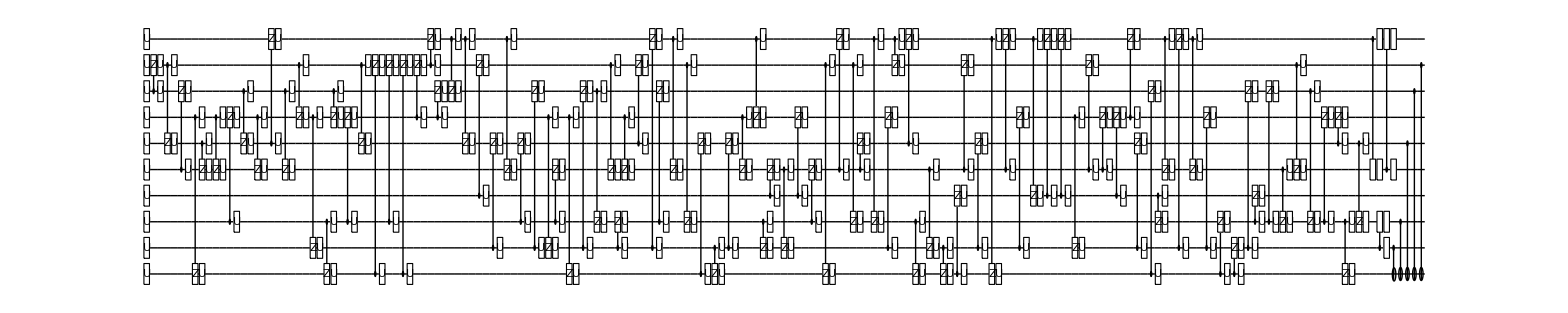

```mathematica
circI=circuitIdeal[numQb,numGt,GateGraph,gates];
DrawCircuit@circI
```

```mathematica
circuitNoisy[numQb_,numGt_,GateGraph_,gates_,model_,ϵ_]:=(
circ={};
Do[(
g=gates[[q+1]];
AppendTo[circ,Subscript[U, q][g]];
),{q,0,numQb-1,1}];
Do[(
q1=GateGraph[[2*t+1]];
q2=GateGraph[[2*t+2]];
AppendTo[circ,Subscript[C, q1][Subscript[Z, q2]]];
If[model==0,AppendTo[circ,Subscript[Depol, q1,q2][ϵ]]];
If[model==1,AppendTo[circ,Subscript[Deph, q1,q2][ϵ]]];
If[model==2,AppendTo[circ,Subscript[Damp, q1][ϵ]];AppendTo[circ,Subscript[Damp, q2][ϵ]]];
g=gates[[numQb+2*t+1]];
AppendTo[circ,Subscript[U, q1][g]];
g=gates[[numQb+2*t+2]];
AppendTo[circ,Subscript[U, q2][g]];
),{t,0,numGt-1,1}];
Do[(
If[GateGraph[[2*numGt+1,q]]==1,AppendTo[circ,Subscript[C, q][Subscript[X, 0]]]];
),{q,1,numQb-1,1}];
Return[circ]
)
```

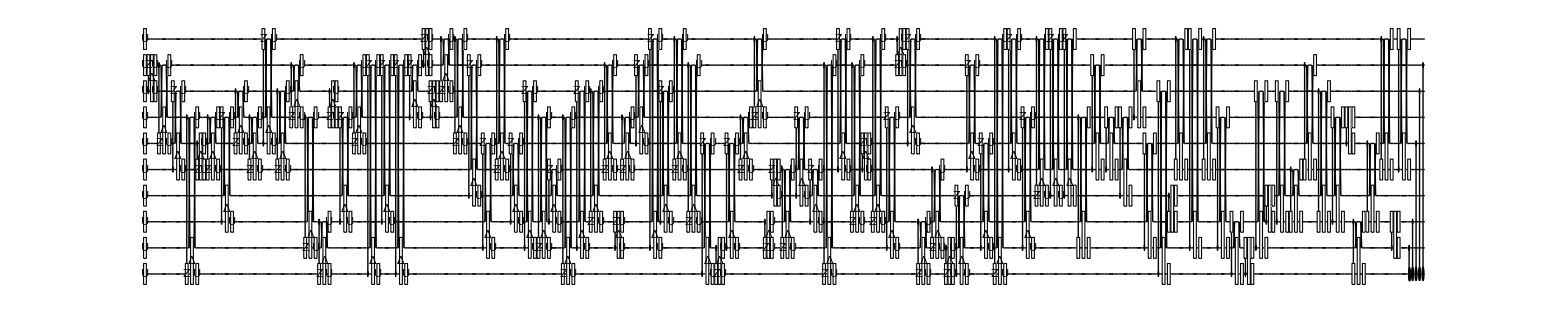

```mathematica
circN=circuitNoisy[numQb,numGt,GateGraph,gates,model,ϵ];
DrawCircuit@circN
```

## Sampling

```mathematica
SamplingU[numQb_,numGt_,GateGraph_,model_,ϵ_,SamSize_]:=(
Err={};
Fid={};
Do[(
gates=RandomVariate[CircularUnitaryMatrixDistribution[2],numQb+2*numGt];
circI=circuitIdeal[numQb,numGt,GateGraph,gates];
circN=circuitNoisy[numQb,numGt,GateGraph,gates,model,ϵ];
ApplyCircuit[circI,ψIN,ψOUT];
ZI=CalcExpecPauliSum[ψOUT,Subscript[Z, 0],ψWP];
ApplyCircuit[circN,ρIN,ρOUT];
ZN=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
AppendTo[Err,ZN-ZI];
AppendTo[Fid,1-CalcFidelity[ρOUT,ψOUT]];
),SamSize];
Return[{Err,Fid}]
)
```

```mathematica
SamplingC[numQb_,numGt_,GateGraph_,model_,ϵ_,SamSize_]:=(
Err={};
Fid={};
Do[(
gates=RandomChoice[Clifford,numQb+2*numGt];
circI=circuitIdeal[numQb,numGt,GateGraph,gates];
circN=circuitNoisy[numQb,numGt,GateGraph,gates,model,ϵ];
ApplyCircuit[circI,ψIN,ψOUT];
ZI=CalcExpecPauliSum[ψOUT,Subscript[Z, 0],ψWP];
ApplyCircuit[circN,ρIN,ρOUT];
ZN=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
AppendTo[Err,ZN-ZI];
AppendTo[Fid,1-CalcFidelity[ρOUT,ψOUT]];
),SamSize];
Return[{Err,Fid}]
)
```

## Simulation

Tue 18 Feb 2020 15:51:27GMT+8.

{0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,{0,0,0,0,0}}

Tue 18 Feb 2020 15:51:27GMT+8.

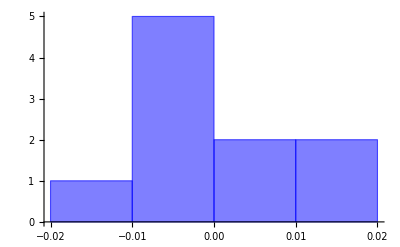

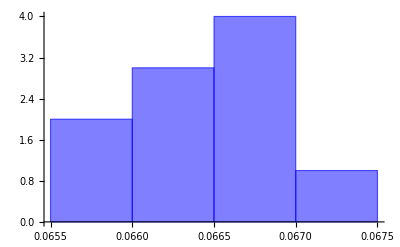

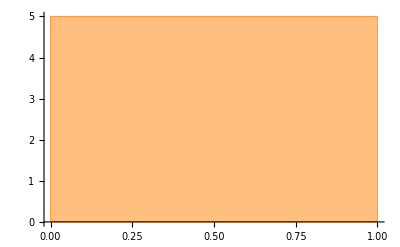

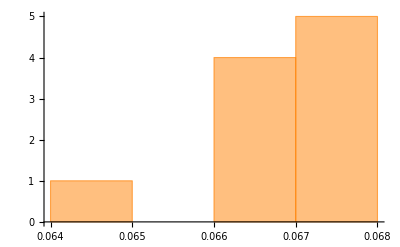

```mathematica
StartTime = Now
GateGraph=GateGraphGen[numQb,numGt,seed]
US=SamplingU[numQb,numGt,GateGraph,model,ϵ,SamSize];
CS=SamplingC[numQb,numGt,GateGraph,model,ϵ,SamSize];
EndTime = Now

Histogram[US[[1]],ChartStyle->Opacity[.5,Blue]]
Histogram[US[[2]],ChartStyle->Opacity[.5,Blue]]
Histogram[CS[[1]],ChartStyle->Opacity[.5,Orange]]
Histogram[CS[[2]],ChartStyle->Opacity[.5,Orange]]

AppendTo[Data,"US-Err:"];AppendTo[Data,US[[1]]];AppendTo[Data,""];
AppendTo[Data,"US-Fid:"];AppendTo[Data,US[[2]]];AppendTo[Data,""];
AppendTo[Data,"CS-Err:"];AppendTo[Data,CS[[1]]];AppendTo[Data,""];
AppendTo[Data,"CS-Fid:"];AppendTo[Data,CS[[2]]];AppendTo[Data,""];
AppendTo[Data,"Start Time: "<>ToString[StartTime]];
AppendTo[Data,"End Time: "<>ToString[EndTime]];
Export[file,Data];
```

```mathematica
MUS=Table[Moment[US[[1]],m],{m,1,10,1}]
MCS=Table[Moment[CS[[1]],m],{m,1,10,1}]
MUS=Table[Moment[US[[2]],m],{m,1,10,1}]
MCS=Table[Moment[CS[[2]],m],{m,1,10,1}]
```

{-0.000304755,0.000051154,7.89697×10^-8,5.94621×10^-9,1.16037×10^-11,7.9745×10^-13,1.20565×10^-15,1.10147×10^-16,9.56036×10^-20,1.53567×10^-20}

{5.15863×10^-17,8.71984×10^-33,1.19606×10^-48,1.93181×10^-64,3.1266×10^-80,5.22351×10^-96,8.80966×10^-112,1.49837×10^-127,2.55943×10^-143,4.38484×10^-159}

{0.066445,0.0044151,0.000293383,0.0000194959,1.29559×10^-6,8.61013×10^-8,5.72224×10^-9,3.8031×10^-10,2.5277×10^-11,1.68007×10^-12}

{0.0667511,0.00445647,0.000297575,0.0000198735,1.32747×10^-6,8.86841×10^-8,5.92567×10^-9,3.96004×10^-10,2.64686×10^-11,1.76942×10^-12}